#### 2.1.1 | Gompertz Equation with Constant Infusion

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;α=2;u=3;
```

```mathematica
p1[t_]= p0^{Exp[-α*t]}*Exp[(Log[k]-(u/α))*(1-Exp[-α*t])]
```

{3^(ⅇ^(-2 t)) ⅇ^((1-ⅇ^(-2 t)) (-3/2+Log[7]))}

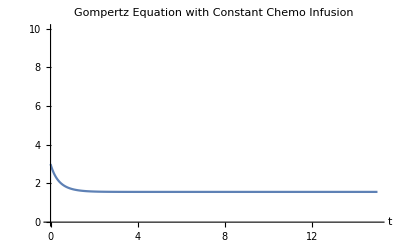

```mathematica
Plot[p1[t],{t,0,15},PlotRange->{0,10},PlotLabel->"Gompertz Equation with Constant Chemo Infusion",AxesLabel -> Automatic]
```